```mathematica
ClearAll["Global`*"]
```

```mathematica
a=1.0;(*vacuum value*)
lambda=1.0;(*coupling*)
m=Sqrt[2 lambda a^2];(*mass around vacuum*)
alpha=m/2.0;(*1/width scale of kink*)

(*Domain and time*)
xmin=-300.0;
xmax=300.0;
tmax=300.0;
```

```mathematica
(*initial kink center and incoming packet*)
Xk0=-30.0;(*kink center initially (left-of-center)*)
Aamp=0.03;(*packet amplitude (small)*)
k0=1.5;(*carrier wavenumber*)
omega0=Sqrt[k0^2+m^2];
sigma=8.0;(*packet spatial width*)
x0packet=xmin+160.0;(*packet initial center (left side)*)
```

```mathematica
(*sponge/damping near boundaries*)dampWidth=40.0;
gammaMax=0.18;
```

```mathematica
(*numerical grid/resolution*)
nx=6001;(*number of spatial points. increase for convergence*)
```

```mathematica
(*--------------------DEFINITIONS--------------------*)phiK[x_,Xc_]:=a*Tanh[alpha*(x-Xc)];(*kink profile*)
phiKp[x_,Xc_]:=D[phiK[y,Xc],y]/. y->x;(*phi_K'*)
Vprime[phi_]:=lambda*phi*(phi^2-a^2);(*V'(phi)*)
VenergyDensity[phi_,phit_,phix_]:=1/2 phit^2+1/2 phix^2+(lambda/4) (phi^2-a^2)^2;

(*normalized shape (internal) mode centered at 0*)
psi1xi[ξ_]:=Sqrt[(3 m)/4]*Sinh[alpha*ξ]/(Cosh[alpha*ξ]^2);

(*smooth damping (sponge) that is zero in central region,ramps up near boundaries*)
gammaFun[x_]:=Module[{left,right},left=If[x<xmin+dampWidth,gammaMax*((xmin+dampWidth-x)/dampWidth)^2,0];
right=If[x>xmax-dampWidth,gammaMax*((x-(xmax-dampWidth))/dampWidth)^2,0];
Max[left,right]];
```

```mathematica
(*--------------------INITIAL DATA--------------------*)initialPhi[x_]:=phiK[x,Xk0]+Aamp*Exp[-(x-x0packet)^2/(2 sigma^2)]*Cos[k0*(x-x0packet)];
initialPhiT[x_]:=+Aamp*omega0*Exp[-(x-x0packet)^2/(2 sigma^2)]*Sin[k0*(x-x0packet)];

(*PDE with sponge damping:phi_tt-phi_xx+V'(phi)+gamma(x) phi_t==0*)
pde=D[phi[t,x],{t,2}]-D[phi[t,x],{x,2}]+Vprime[phi[t,x]]+gammaFun[x]*D[phi[t,x],t]==0;

(*boundary conditions:set to vacua consistent with kink interpolation*)
bcs={phi[t,xmin]==-a,phi[t,xmax]==a};

(*initial conditions*)
ics={phi[0,x]==initialPhi[x],(D[phi[t,x],t]/. t->0)==initialPhiT[x]};
```

```mathematica
(*--------------------SOLVE PDE--------------------*)Print["Starting NDSolve..."];
(*Using MethodOfLines with tensor grid spatial discretization and BDF time integrator*)
sol=NDSolve[{pde,bcs,ics},phi,{t,0,tmax},{x,xmin,xmax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->nx,"MaxPoints"->nx,"DifferenceOrder"->4},"TemporalVariable"->t},MaxSteps->Infinity,WorkingPrecision->MachinePrecision,EvaluationMonitor:>Null,
Method->{"BDF","MaxDifferenceOrder"->2},(*reduce if needed*)AccuracyGoal->6,PrecisionGoal->8];

If[sol==={},Print["NDSolve failed — try reducing nx or tmax or switch integrator."];Abort[]];

phiSol[t_,x_]:=Evaluate[phi[t,x]/. First[sol]];

Print["NDSolve finished."];
```

Starting NDSolve...

NDSolve finished.

```mathematica
(*-----Quick check:evaluate phi at sample (t,x)-----*)(*Example:phiSol[0,Xk0] should be~0 (kink center),phiSol[0,x0packet]~packet amplitude+/-*)Print["phiSol[0, Xk0] = ",phiSol[0,Xk0]];
Print["phiSol[0, x0packet] = ",phiSol[0,x0packet]];
```

phiSol[0, Xk0] = -4.81482×10^-35

phiSol[0, x0packet] = -0.97

```mathematica
(*-----B) Interactive slider using Manipulate-----*)(*NOTE:interactive slider will repeatedly evaluate phiSol[t,x].For responsiveness,lower'PlotRange' sampling or use smaller nx.*)Print["Opening interactive slider (Manipulate). For large nx this may be slower—reduce nx for snappier interactivity."];
Manipulate[Plot[Evaluate[phiSol[t0,x]],{x,xmin,xmax},PlotRange->{-1.2 a,1.2 a},AxesLabel->{"x","ϕ(x,t)"},PlotLabel->Row[{"\!\(\*SubscriptBox[\(ϕ\), \((x,t)\)]\) at t = ",NumberForm[t0,{5,2}]}],ImageSize->Large,PerformanceGoal->"Quality"],{{t0,0,"time t"},0,tmax,Appearance->"Labeled"},ControlPlacement->Top]
```

Opening interactive slider (Manipulate). For large nx this may be slower—reduce nx for snappier interactivity.

```mathematica
(*-----DIAGNOSTICS/POSTPROCESSING-----*)(*build a spatial sampling grid (for quick interpolation)*)xGrid=Subdivide[xmin,xmax,nx-1];

(*function to get an interpolating function of phi at time t (speeds repeated calls)*)
phiInterpAtT[tt_]:=Module[{vals,f},vals=Table[{xx,phiSol[tt,xx]},{xx,xGrid}];
f=Interpolation[vals,InterpolationOrder->3];
f];

(*find kink center X(t) by locating phi=0 crossing near previous center*)
findKinkCenter[tt_,Xguess_,phiInterp_]:=Module[{left,right,xs,fs,idx,apts,root},left=Max[xmin,Xguess-20];
right=Min[xmax,Xguess+20];
xs=Subdivide[left,right,400];
fs=phiInterp/@xs;
idx=FirstPosition[Partition[fs,2,1],{u_,v_}/;u*v<=0,Missing[]];
If[idx===Missing[],(*no sign change near guess->return guess (kink possibly disrupted)*)Xguess,apts={xs[[idx[[1]]]],xs[[idx[[1]]+1]]};
root=x/. FindRoot[phiInterp[x]==0,{x,apts[[1]],apts[[2]]},MaxIterations->50];
root]];
```

```mathematica
(*function to compute shape-mode overlap A1(t) with instantaneous center Xc*)A1AtT[tt_,Xc_,phiInterp_]:=Module[{integrand},integrand=Function[{x},psi1xi[x-Xc]*(phiInterp[x]-phiK[x,Xc])];
NIntegrate[integrand[x],{x,xmin,xmax},WorkingPrecision->12,MaxRecursion->20]];
(*field momentum and energy*)PfieldAtT[tt_,phiInterp_]:=Module[{phit,phix},phit[x_]:=Evaluate[D[phi[t,x],t]/. t->tt/. First[sol]];
phix[x_]:=D[phiInterp[x],x];
NIntegrate[phit[x]*phix[x],{x,xmin,xmax},WorkingPrecision->12,MaxRecursion->20]];

EnergyAtT[tt_,phiInterp_]:=Module[{phit,phix},phit[x_]:=Evaluate[D[phi[t,x],t]/. t->tt/. First[sol]];
phix[x_]:=D[phiInterp[x],x];
NIntegrate[VenergyDensity[phiInterp[x],phit[x],phix[x]],{x,xmin,xmax},WorkingPrecision->12,MaxRecursion->20]];
```

```mathematica
(*detectors for left/right signals*)
xLeftDetect=xmin+80;
xRightDetect=xmax-80;
(*time sampling for diagnostics (coarse)*)
nt=201;
timesList=Subdivide[0.,tmax,nt-1];
```

```mathematica
Print["Computing diagnostics across time grid..."];

kinkCenters=ConstantArray[0.,nt];
A1vals=ConstantArray[0.,nt];
Pvals=ConstantArray[0.,nt];
Evals=ConstantArray[0.,nt];

Xguess=Xk0;
Do[tt=timesList[[ii]];
phInterp=phiInterpAtT[tt];
Xc=findKinkCenter[tt,Xguess,phInterp];
kinkCenters[[ii]]=Xc;
Xguess=Xc;
A1vals[[ii]]=A1AtT[tt,Xc,phInterp];
Pvals[[ii]]=PfieldAtT[tt,phInterp];
Evals[[ii]]=EnergyAtT[tt,phInterp];
If[Mod[ii,20]==0,Print["  progress: ",NumberForm[100 ii/nt,{3,1}],"% (t=",NumberForm[tt,{4,1}],")"]],{ii,1,nt}];

Print["Diagnostics computed."];

(*kink velocity from time differences*)
vKink=Differences[kinkCenters]/Differences[timesList];
tmid=MovingAverage[timesList,2];

(*detector time series (dense sample)*)
denseNT=2048;(*power of 2 helps FFT*)denseTimes=Subdivide[0.,tmax,denseNT-1];
phiLeftSeries=Table[phiSol[tt,xLeftDetect],{tt,denseTimes}];
phiRightSeries=Table[phiSol[tt,xRightDetect],{tt,denseTimes}];

(*FFT magnitude (absolute)-show frequency content*)
fftLeft=Abs[Fourier[phiLeftSeries]];
fftRight=Abs[Fourier[phiRightSeries]];
freqs=Table[(i-1)/tmax,{i,Length[fftLeft]}];
```

Computing diagnostics across time grid...

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in x near {x} = {-30.8996267623}. NIntegrate obtained 2.61588253874×10^-7 and 1.09372562727×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in x near {x} = {-30.8996267623}. NIntegrate obtained 1.07890345188×10^-9 and 7.7555938904×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in x near {x} = {-30.8996267623}. NIntegrate obtained -1.63465929011×10^-7 and 7.58760676062×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

progress: 2000/201% (t=28.5)

progress: 4000/201% (t=58.5)

progress: 2000/67% (t=88.5)

progress: 8000/201% (t=118.5)

progress: 10000/201% (t=148.5)

progress: 4000/67% (t=178.5)

progress: 14000/201% (t=208.5)

progress: 16000/201% (t=238.5)

progress: 6000/67% (t=268.5)

progress: 20000/201% (t=298.5)

Diagnostics computed.

Generating plots...

Showing plots...

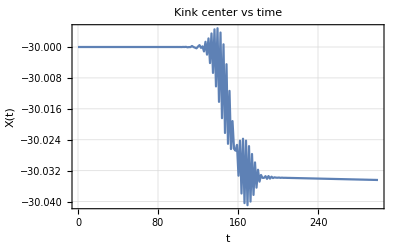

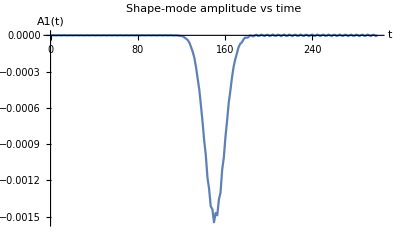

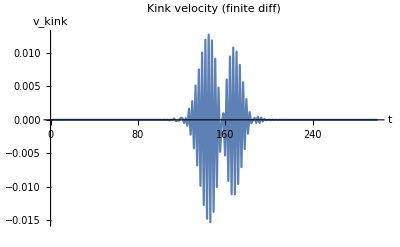

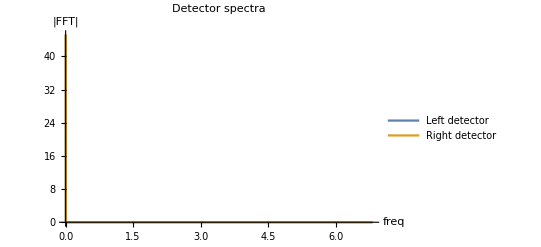

```mathematica
(*--------------------PLOTS--------------------*)Print["Generating plots..."];

p1=ListLinePlot[Transpose[{timesList,kinkCenters}],PlotRange->All,AxesLabel->{"t","X(t)"},PlotTheme->"Detailed",PlotLabel->"Kink center vs time"];

p2=ListLinePlot[Transpose[{timesList,A1vals}],PlotRange->All,AxesLabel->{"t","A1(t)"},PlotLabel->"Shape-mode amplitude vs time"];

p3=ListLinePlot[Transpose[{tmid,vKink}],PlotRange->All,AxesLabel->{"t","v_kink"},PlotLabel->"Kink velocity (finite diff)"];

p4=ListLinePlot[{Transpose[{freqs,fftLeft}],Transpose[{freqs,fftRight}]},PlotRange->All,AxesLabel->{"freq","|FFT|"},PlotLegends->{"Left detector","Right detector"},PlotLabel->"Detector spectra"];

Print["Showing plots..."];
Print[p1];
Print[p2];
Print[p3];
Print[p4];
```

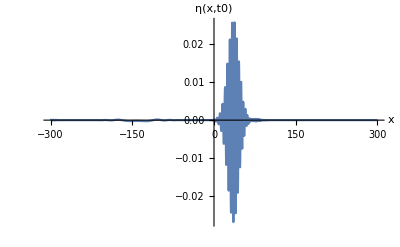

```mathematica
(*get instantaneous center Xc at time t0 using your root-finder or interpolation*)
t0=240;(*e.g.60*)
Xc=findKinkCenter[t0,-30,phiInterpAtT[t0]];(*reuse your existing routine*)eta[x_]:=phiSol[t0,x]-a*Tanh[alpha*(x-Xc)];
Plot[eta[x],{x,xmin,xmax},PlotRange->All,AxesLabel->{"x","η(x,t0)"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

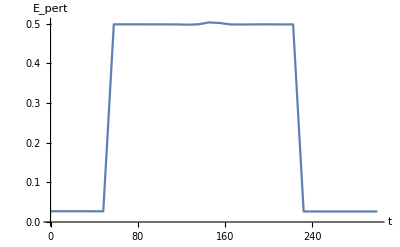

```mathematica
(*define derivatives from solution*)phiT[t_,x_]:=Evaluate[D[phi[t,x],t]/. phi->phiSol];
phiX[t_,x_]:=Evaluate[D[phi[t,x],x]/. phi->phiSol];

energyPerturbationAtT[tt_]:=NIntegrate[Module[{Xc=kinkCenterAtT[tt,Xk0],ph=phiSol[tt,x],phK=a*Tanh[alpha*(x-Xc)]},1/2*((phiT[tt,x])^2+(phiX[tt,x])^2)+(lambda/4)*(ph^2-a^2)^2-(lambda/4)*(phK^2-a^2)^2-(lambda*phK*(phK^2-a^2))*(ph-phK) (* =V'(\phi_K)*(phi-phi_K)*)],{x,xmin,xmax},WorkingPrecision->10,MaxRecursion->20];

times=Subdivide[0,tmax,31];
Epert=Table[energyPerturbationAtT[tt],{tt,times}];
ListLinePlot[Transpose[{times,Epert}],AxesLabel->{"t","E_pert"}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-139.4762746}. NIntegrate obtained 0.02714125161 and 0.00001001250483 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-107.8356496}. NIntegrate obtained 0.02703357458 and 0.00001331827083 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-29.32002465}. NIntegrate obtained 0.9697066461 and 0.0005970809428 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-139.4762746}. NIntegrate obtained -0.01972732375 and 0.00001353285264 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-107.8356496}. NIntegrate obtained -0.01965515151 and 0.00001670399849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-73.85127465}. NIntegrate obtained -0.01956775923 and 0.00001533369373 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

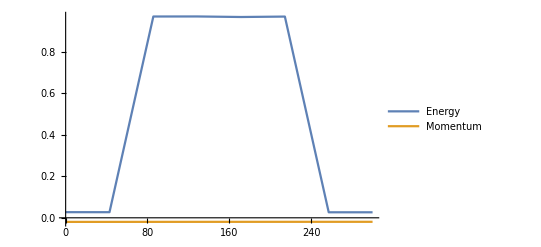

```mathematica
totalEnergyAtT[tt_] := NIntegrate[
  1/2*(phiT[tt, x]^2 + phiX[tt, x]^2) + (lambda/4)*(phiSol[tt, x]^2 - a^2)^2,
  {x, xmin, xmax}, WorkingPrecision -> 10
];
totalMomAtT[tt_] := NIntegrate[phiT[tt, x]*phiX[tt, x], {x, xmin, xmax}, WorkingPrecision -> 10];

timesSmall = Subdivide[0, tmax, 7];
Efull = Table[totalEnergyAtT[tt], {tt, timesSmall}];
Pfull = Table[totalMomAtT[tt], {tt, timesSmall}];
ListLinePlot[{Transpose[{timesSmall, Efull}], Transpose[{timesSmall, Pfull}]},
 PlotLegends -> {"Energy", "Momentum"}]
```

NIntegrate::precw: The precision of the argument function (+<<333581152 bytes>>) is less than WorkingPrecision (30.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in x near {x} = {-30.4996502903471872878797334116}. NIntegrate obtained 0.96995326983553667842002351915 and 1.5851085928596322612953631651×10^-9 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (+<<333581152 bytes>>) is less than WorkingPrecision (30.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in x near {x} = {-30.4996502903471872878797334116}. NIntegrate obtained 0.969918762159694461125058135414 and 1.53821020019657076298294746185×10^-9 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (+<<333581152 bytes>>) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in x near {x} = {-30.4996502903471872878797334116}. NIntegrate obtained 0.969880521140805754090683928247 and 1.65587430932074807435897641771×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.325033456635748801168700617938353326834597011836468899694621175065485996508837×10^-63 and 7.276217041688751904628940894148293538043546559628346260939222727886394194871329×10^-64 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.0859742425287242605696912063835297219103673509964228332531530204863691357755091×10^-22 and 8.5428749186476240564692237416575894613885114488754514801887513887981201527770434×10^-28 for the integral and error estimates.

$Aborted

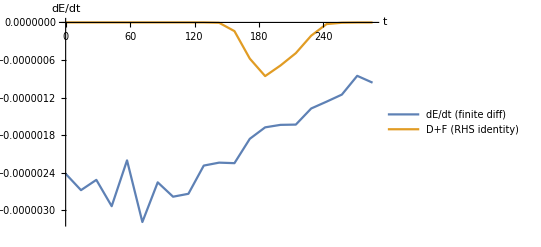

E(t_end) = 0.969336646266427441912576392752

dE/dt (last interval) = -9.61493×10^-7

D+F (last sample) = -1.29241×10^-9

```mathematica
(*---helpers:time-deriv and space-deriv of phi from the InterpolatingFunction---*)phiT[t_,x_]:=Evaluate[D[phi[t,x],t]/. phi->phiSol];
phiX[t_,x_]:=Evaluate[D[phi[t,x],x]/. phi->phiSol];
phiTT[t_,x_]:=Evaluate[D[phi[t,x],{t,2}]/. phi->phiSol];
phiXX[t_,x_]:=Evaluate[D[phi[t,x],{x,2}]/. phi->phiSol];

(*---energy,dissipation,flux definitions---*)
energyAtT[t_]:=NIntegrate[1/2 phiT[t,x]^2+1/2 phiX[t,x]^2+(lambda/4)*(phiSol[t,x]^2-a^2)^2,{x,xmin,xmax},WorkingPrecision->30,MaxRecursion->20];

dissipationAtT[t_]:=-NIntegrate[gammaFun[x]*phiT[t,x]^2,{x,xmin,xmax},WorkingPrecision->30,MaxRecursion->20];
fluxAtT[t_]:=(phiT[t,x]*phiX[t,x])/. x->xmax-(phiT[t,x]*phiX[t,x])/. x->xmin;

(*sample times*)
times=Subdivide[0,tmax,21];(*coarse;increase for more fidelity*)(*compute arrays*)Evals=Table[energyAtT[tt],{tt,times}];
Dvals=Table[dissipationAtT[tt],{tt,times}];
Fvals=Table[fluxAtT[tt],{tt,times}];

(*numerical time derivative of E*)
dEapprox=Differences[Evals]/Differences[times];

(*compare identity:dE/dt?=D+F (note dEapprox has length one less than Dvals,Fvals)*)
ListLinePlot[{Transpose[{Most[times],dEapprox}],Transpose[{Most[times],Most[Dvals]+Most[Fvals]}]},PlotLegends->{"dE/dt (finite diff)","D+F (RHS identity)"},AxesLabel->{"t","dE/dt"}]

(*Print some numbers for the last sampled time*)
Print["E(t_end) = ",Last[Evals]];
Print["dE/dt (last interval) = ",dEapprox[[-1]]];
Print["D+F (last sample) = ",(Last[Dvals]+Last[Fvals])];
```

```mathematica
Print["Max flux magnitude: ",Max[Abs[Fvals]]];
Print["Max dissipation magnitude: ",Max[Abs[Dvals]]];
Print["Flux sign samples: ",Table[{times[[i]],Fvals[[i]]},{i,Length[times]}]];
```

Max flux magnitude: 0.

Max dissipation magnitude: 8.56358857940044146085132495601×10^-7

Flux sign samples: {{0.,0.},{14.2857,0.},{28.5714,0.},{42.8571,0.},{57.1429,0.},{71.4286,0.},{85.7143,0.},{100.,0.},{114.286,0.},{128.571,0.},{142.857,0.},{157.143,0.},{171.429,0.},{185.714,0.},{200.,0.},{214.286,0.},{228.571,0.},{242.857,0.},{257.143,0.},{271.429,0.},{285.714,0.},{300.,0.}}

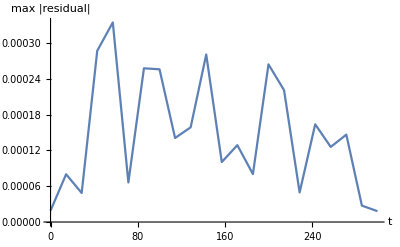

Max residual across times = 0.000334695

```mathematica
residualAtT[t_] := Module[{res, xs},
  xs = Subdivide[xmin, xmax, 801];  (* grid points for residual check *)
  res = Table[Abs[phiTT[t, x] - phiXX[t, x] + lambda*phiSol[t, x]*(phiSol[t, x]^2 - a^2) + gammaFun[x]*phiT[t, x]], {x, xs}];
  Max[res]
];

resvals = Table[residualAtT[tt], {tt, times}];
ListLinePlot[Transpose[{times, resvals}], AxesLabel -> {"t", "max |residual|"}]
Print["Max residual across times = ", Max[resvals]];
```